### Global Order parameters

```mathematica
SetDirectory[NotebookDirectory[]];
polorder = Import["data/polorder.mx"];
nemorder = Import["data/nemorder.mx"];
tmax = 4761.9;
snapcount2 = 1001;
time2=Range[0,tmax,tmax/(snapcount2-1)];
```

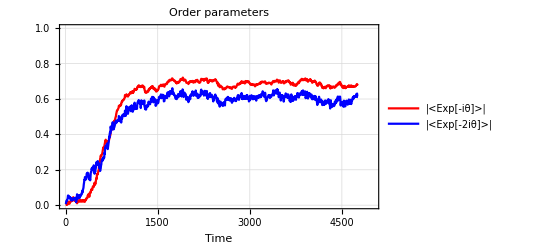

```mathematica
ListLinePlot[{{time2,polorder}//Thread,{time2,nemorder}//Thread},PlotRange->{{0,5000},{0,1}},Frame->True,PlotStyle->{{Red},{Blue}},GridLines->Automatic,PlotLegends->Placed[{Style["|<Exp[-iθ]>|",12],Style["|<Exp[-2iθ]>|",12]},{0.78,0.40}],FrameLabel->{Style["Time",14]},PlotLabel->Style["Order parameters",14]]
```